# Bloque 1 - Introducción al lenguaje

### Autor: Carlos Manuel Rodríguez Martínez Email: fis.carlosmanuel@gmail.com

## Introducción

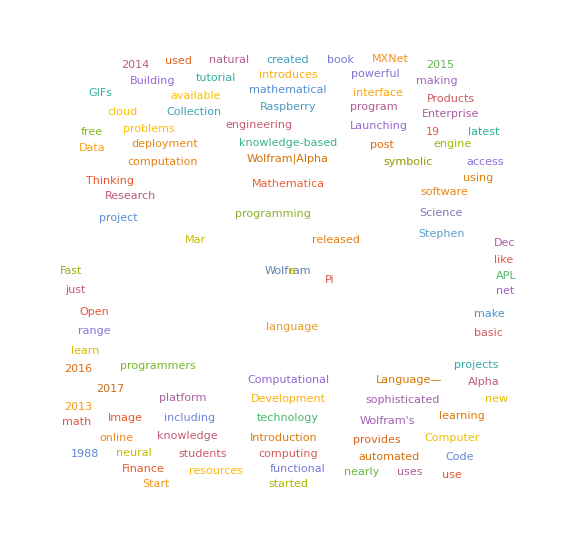

```mathematica
googleCS=ServiceConnect["GoogleCustomSearch"];
results=googleCS["Search",{"Query"->"Wolfram language",MaxItems->200}];
WordCloud[DeleteStopwords[Flatten[Join[Map[TextWords,Normal[results[All,"Snippet"]]]]]]]
```

Posiblemente el lenguaje de más alto nivel

Fuente: http://blog.wolfram.com/2016/11/09/the-2016-wolfram-one-liner-competition-winners/

```mathematica
i = RandomImage[];
Dynamic[Magnify[i = NetInitialize[NetChain[{ConvolutionLayer[3,3],Tanh},"Input"->"Image","Output"->"Image"]][i],3]]
```

Todo es una expresión simbólica

```mathematica
imagen = -Graphics-;
```

```mathematica
ImageRotate[imagen,π/6]
```

-Graphics-

```mathematica
val = 1.9;
ImageTransformation[imagen,{Re[#],Im[#]}&[val/(1+I-val{1,I}.#)]&,600,Padding->"Reflected"]
```

-Graphics-

Funcional

```mathematica
a = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Map[#^2&,a]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
b = Partition[Range[20],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20}}

```mathematica
MapAt[#^2&,b,{All,2}]
```

{{1,4},{3,16},{5,36},{7,64},{9,100},{11,144},{13,196},{15,256},{17,324},{19,400}}

Basado en el conocimiento

WolframAlphaQueryParseResults

-Graphics-

WolframAlphaQueryParseResults

Xalapa

```mathematica
CityData[Entity["City",{"Xalapa","Veracruz","Mexico"}],"Coordinates"]
```

{19.53,-96.92}

```mathematica
Entity["City",{"Xalapa","Veracruz","Mexico"}]["Population"]
```

387879 people

```mathematica
EntityList[EntityClass["Country","Countries"]]
```

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Swaziland,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
EntityList["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

Interactivo

```mathematica
a = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Manipulate[Map[#^i&,a],{i,1,2}]
```

```mathematica
Manipulate[ListPlot[Map[#^i&,a],PlotRange->{{0,11},{0,100}}],{i,1,2}]
```

Extensamente documentado

La documentación se encuentra en: Ayuda -> Documentación
Muchos problemas específicos se encuentran resueltos en: https://mathematica.stackexchange.com/
Otra buena fuente de prácticas resueltas está en: http://demonstrations.wolfram.com/

## Sintaxis básica y funciones

Expresiones

En la interfaz notebook de Mathematica existen dos tipos de entrada: código y texto. Las opciones para alternar entre código y texto se encuentran en Format -> Style. El código se puede ejecutar con Shift+Enter. La interfaz de notebook actúa como un front- end, que se encarga de enviar el código ejecutado al kernel.

En el lenguaje Wolfram todo son expresiones. Las expresiones pueden consistir en números como:

Enteros

```mathematica
5
```

5

Números reales

```mathematica
230.4
```

230.4

Números complejos

```mathematica
2+ⅈ
```

2+ⅈ

Racionales

```mathematica
3/2
```

3/2

Cadenas de texto:

```mathematica
"Hello world"
```

Hello world

Y símbolos, los cuales se pueden asignar

```mathematica
x
```

x

```mathematica
α = 1
```

1

```mathematica
α
```

1

Los símbolos siempre deben empezar por un carácter,  si se coloca un dígito en la primera posición en vez de un carácter Mathematica lo interpreta como una multiplicación

```mathematica
2α
```

También existen las funciones, que se encargan de realizar procedimientos

```mathematica
Sqrt[9]
```

3

Nota 1

Para introducir los símbolos especiales se usa la tecla Esc. Por ejemplo, para α se pulsa Esc + a + Esc.

Nota 2

Es muy importante hacer notar que como todos son expresiones, todo, incluso los símbolos. Es por eso que es posible dar un símbolo no asignado como argumento de una función. En lenguajes compilados como C++ esto sería imposible.

```mathematica
f[x]
```

f[x]

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

Al asignar una expresión esta se guarda en el espacio global del kernel. Si es necesario se puede borrar la definición usando la función Clear.

```mathematica
Clear[α]
```

Para realizar cálculos numéricos no es recomendable el uso de números racionales. Para convertir estos en números reales se utiliza la función N.

```mathematica
N[4/9]
```

0.444444

Para ocultar el resultado escribimos punto y coma al final del statement.

```mathematica
var = 6;
```

### Nota:

Para evaluar funciones siempre se usan los corchetes cuadrados [ ] mientras que para agrupar expresiones se utilizan los paréntesis ()

```mathematica
Times[Plus[3,5],4]
```

32

```mathematica
(3+5)*4
```

32

### Ejercicio:

Calcule 10 elevado a la 12. Primero evalúe utilizando el operador potencia ^, luego realice la misma operación pero utilizando las representaciones que se encuentran en Paletas -> Ayudante de clase.

Propiedades de las expresiones

A los elementos del tipo numérico, texto y demás que no pueden ser simplificados más allá se les denomina expresiones atómicas, esto es, expresiones que no pueden ser subdivididas. Una manera de conocer si una expresión es atómica es usando la función AtomQ.

Un símbolo sin asignar es una expresión atómica porque no puede simplificarse más.

```mathematica
AtomQ[x]
```

True

Mientras que dos símbolos con un operador de suma no es una expresión atómica.

```mathematica
AtomQ[x+3]
```

False

Es posible inspeccionar una expresión en su forma completa utilizando la función FullForm[], se observa que la expresión x+3 se evalúa en realidad como una función llamada Plus con dos (o más) argumentos, de manera que se puede subdividir más.

```mathematica
FullForm[x+3]
```

Plus[3,x]

Mientras que al evaluar un símbolo sin asignar no hay ninguna expresión extra.

```mathematica
FullForm[x]
```

x

Las expresiones están compuestas por un encabezado que indica el tipo de expresión, y el contenido, el cual es manejado y optimizado por el kernel. Se puede ver el encabezado usando la función Head.

```mathematica
Head[x]
```

Symbol

```mathematica
Head[3]
```

Integer

```mathematica
Head["hello world"]
```

String

```mathematica
Head[3.3]
```

Real

### Nota

Una de las ventajas de programar usando un lenguaje interpretado es que no es necesario preocuparse por algunas propiedades relacionadas con el manejo de memoria. Por ejemplo, en lenguajes como C++ sólo se pueden almacenar números enteros en el rango entre

```mathematica
2^31
```

2147483648

y

```mathematica
-2^31
```

-2147483648

Esto es debido a que el número se representa en la memoria como una cadena de bits de un tamaño fijo de 32. Esto da una gran ventaja en velocidad, pero también es una limitación. Mathematica puede manejar números de tamaño y precisión arbitraria (internamente utiliza GMP), de manera que puede devolver resultados como este:

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

### Ejercicios:

#### Ejercicio 1:

¿Qué ocurre cuando se asigna un valor a x y luego se observa su encabezado? ¿Por qué ocurre eso?

#### Ejercicio 2:

Anteriormente se mencionó que para realizar cálculos numéricos no es recomendable el uso de números racionales. Supongamos entonces que deseamos realizar la suma entre 2/3 y 4, compare qué ocurre internamente cuando se usan números racionales y cuando se convierte el número racional a la forma numérica.

Listas

Se pueden definir listas con varios tipos de expresiones, como por ejemplo

```mathematica
list = {1,x,"a string",7/8}
```

{1,x,a string,7/8}

Cuando se define una lista se crea una expresión con el encabezado de lista,

```mathematica
Head[list]
```

List

En realidad una lista no es más que una función del tipo lista con varios argumentos. Esta función no calcula nada de forma directa, pero es utilizada de forma interna por el kernel para reconocer el tipo de la expresión.

```mathematica
FullForm[list]
```

List[1,x,"a string",Rational[7,8]]

En una lista se puede acceder a cada elemento por su índice (comenzando a partir de 1)

```mathematica
list[[1]]
```

1

```mathematica
list[[2]]
```

x

Los índices también pueden ser negativos.

```mathematica
list[[-1]]
```

7/8

Para conocer el tamaño de una lista se usa la función Length.

```mathematica
Length[list]
```

4

Se pueden acceder a varios elementos simultáneos de una lista por medio del operador Span (  ;;  ) y del operador Part (  [[]]  ), por ejemplo

```mathematica
{a,b,c,d,e,f,g,h}[[2;;4]]
```

{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20}},c,d}

```mathematica
FullForm[Hold[{a,b,c,d,e,f,g,h}[[2;;4]]]]
```

Hold[Part[List[a,b,c,d,e,f,g,h],Span[2,4]]]

nos devuelve los elementos desde el índice 2 al índice 5. También se puede especificar el intervalo de salto, como por ejemplo, tomar los elementos del 1 al 6 dando saltos de 2 en 2.

```mathematica
{a,b,c,d,e,f,g,h}[[1;;6;;2]]
```

{{1,2,3,4,5,6,7,8,9,10},c,e}

En caso de tener listas bidimensionales se puede hacer uso de la propiedad All del operador Part para acceder a cada unas de las columnas.

```mathematica
{{1,2},{3,4},{5,6}}[[All,1]]
```

{1,3,5}

```mathematica
{{1,2,3},{4,5,6},{7,8,9}}[[All,2]]
```

{2,5,8}

Se puede también obtener varios índices específicos de las sublistas.

```mathematica
{{1,2,3},{4,5,6},{7,8,9}}[[All,{1,2}]]
```

{{1,2},{4,5},{7,8}}

Por lo general utilizar el operador Part no es una opción muy elegante debido a que hace el código menos legible. Hay funciones que permiten acceder a elementos específicos de la lista, como First[] que devuelve el primer elemento

```mathematica
First[list]
```

1

Last[] que devuelve el último

```mathematica
Last[list]
```

7/8

O Rest[] que devuelve todos excepto el primero.

```mathematica
Rest[list]
```

{x,a string,7/8}

En caso de no tener más opción que utilizar el operador Part, es recomendable utilizar la forma funcional respecto a la forma de operador.

```mathematica
Part[list,3]
```

a string

#### Ejercicio 1:

Existe una gran cantidad de funciones que se pueden utilizar para crear y manipular listas. La función Range nos permite crear listas en un rango especificado.

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Reverse nos permite invertir una lista

```mathematica
Reverse[Alphabet[]]
```

{z,y,x,w,v,u,t,s,r,q,p,o,n,m,l,k,j,i,h,g,f,e,d,c,b,a}

Join nos permite concatenar varias listas

```mathematica
Join[{"a","b"},{"c","d"}]
```

{a,b,c,d}

A partir de esto use Range, Reverse y Join para crear la lista {1,2,3,4,4,3,2,1}.

#### Ejercicio 2:

RandomInteger[] nos devuelve un número entero aleatorio. Podemos especificar su valor máximo en el argumento. Por defecto se genera un aleatorio entre el 0 y 1.

```mathematica
RandomInteger[]
```

1

Pero también es posible generar un entero aleatorio entre el 0 y 5.

```mathematica
RandomInteger[5]
```

3

A partir de esto cree una lista de números sucesivos (con Range) con una longitud aleatoria de hasta 10 entradas.

#### Ejercicio 3:

Dada la matriz

```mathematica
m=Partition[Range[12],4];
MatrixForm[m]
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12)

Intercambie la segunda y tercera fila, y la segunda y la tercera columna de forma que quede

```mathematica
MatrixForm[{{1,3,2,4},{9,11,10,12},{5,7,6,8}}]
```

(1 | 3 | 2 | 4
9 | 11 | 10 | 12
5 | 7 | 6 | 8)

Listas en otros lenguajes

Otros lenguajes de programación suelen referirse a las listas como arrays. El funcionamiento de los arrays varía según el tipo de lenguaje. Por ejemplo C++ sólo permite arrays de un tipo específico, es decir, arrays de puros números enteros, o de puros caracteres de texto.

-Graphics-

Esto es debido a que en C++ cuando se crea un array el programa hace una llamada al sistema operativo pidiendo una reservación de memoria. El sistema operativo responde indicando la posición de la memoria libre para almacenar ese array, y esto implica que el tamaño del array debe ser conocido de antemano implicando que sólo será válido para un tipo específico de datos.

Los lenguajes interpretados como WL o Python no poseen esta limitación (por lo general) ya que la máquina virtual se encarga de gestionar automáticamente el manejo de la memoria.

Reglas de estilo para listas

Al trabajar con listas es posible crear código poco legible. Un ejemplo es el siguiente:

```mathematica
list = Range[10]
{subl1,subl2,subl3} = {list[[1]],list[[2;;-1]],list[[-1]]}
```

{1,2,3,4,5,6,7,8,9,10}

{1,{2,3,4,5,6,7,8,9,10},10}

Una mejor práctica sería utilizando funciones específicas (no siempre aplica) dado que es inmediatamente claro la operación que realizan.

```mathematica
{subl1,subl2,subl3} = {First[list],Rest[list],Last[list]}
```

{1,{2,3,4,5,6,7,8,9,10},10}

Gráficas de listas

Las listas son una de las cosas más fáciles de graficar debido a que sólo es necesario hacer una llamada a la función adecuada.

```mathematica
l = {1,3,5,4,1,2,1,4};
```

```mathematica
Transpose[{Range[Length[l]],l}]
```

{{1,1},{2,3},{3,5},{4,4},{5,1},{6,2},{7,1},{8,4}}

Existen diferentes tipos de gráficas para listas, como ListPlot que muestra los puntos, BarChart que es una gráfica de barras y PieChart, una gráfica circular.

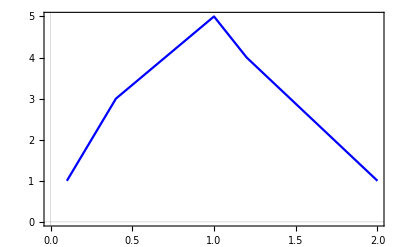

```mathematica
ListPlot[{{0.1,1},{0.4,3},{1,5},{1.2,4},{2,1}},Joined-> True,PlotTheme->"Scientific",PlotStyle->Blue]
```

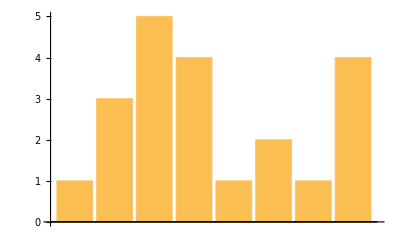

```mathematica
BarChart[l]
```

```mathematica
PieChart[l]
```

-Graphics-

#### Ejercicio 1:

Graficar la lista formada por tres uniones sucesivas de una lista de enteros que va desde el 0 al 20. El resultado esperado es el siguiente:

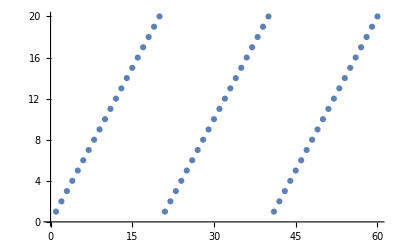

#### Ejercicio 2:

En un experimento del laboratorio de electromagnetismo con Paty se midió la resistencia en ohms de una pieza conductora respecto al área de conducción. Los datos se encuentran en los archivos areas.dat y resistencias.dat. Graficar la relación entre área y resistencia y ajustar un modelo por medio de una función de ajuste como Fit[]. No se vale copiar los datos manualmente, para cargar los archivos se puede usar la función Import[].

Si se desea cargar un archivo que se encuentre junto a la libreta de Mathematica se puede utilizar NotebookDirectory[], por ejemplo

```mathematica
NotebookDirectory[]
```

/home/carlos/Documentos/Programacion/CursoProgramacionCientifica/Unidad 1/

```mathematica
FileNameJoin[{NotebookDirectory[],"archivo.dat"}]
```

/home/carlos/Documentos/Programacion/CursoProgramacionCientifica/Unidad 1/archivo.dat

FileNameJoin es importante para poder usar el mismo código en varios sistemas operativos.

Operadores

Se pueden combinar varias expresiones por medio de operadores. Un ejemplo de operador es el símbolo de adición +. Cuando se realiza una suma, Mathematica nos devuelve el resultado.

```mathematica
2+2
```

4

o

```mathematica
x+y
```

x+y

En realidad, internamente el kernel se encarga de interpretar los operadores y por medio de una regla de sustitución reemplaza el operador por una función. La forma real de la expresión se puede obtener con la función FullForm.

```mathematica
FullForm[x+y]
```

Plus[x,y]

Nótese que el encabezado de una suma es la función Plus.

```mathematica
Head[x+y]
```

Plus

Los operadores funcionan también con expresiones más complejas.

```mathematica
FullForm[(x+y^2)*z]
```

Times[Plus[x,Power[y,2]],z]

El lenguaje Wolfram cuenta con una multitud de operadores de diversos tipos, pero se pueden dividir principalmente en tres tipos:

Operadores Prefix - Son los que preceden a una expresión

```mathematica
!False
```

True

```mathematica
f@x
```

f[x]

Y se representan internamente con

```mathematica
Prefix[f[x]]
```

f@x

Operadores Infix - Son los que se encuentran en medio de dos expresiones

```mathematica
4+5
```

9

Se representan internamente con

```mathematica
Infix[f[x,y,z],"#"]
```

x#y#z

Operadores Postfix - Se encuentran después de una expresión

```mathematica
Postfix[f[x]]
```

x//f

Cuando el kernel termina de ejecutar las funciones, devuelve los resultados en forma Prefix[], Infix[] o Postfix[], y la interfaz de notebook se encarga de darles formato.

Incluso operaciones simples como el ; al final de un statement para evitar que muestre el resultado de la evaluación es en realidad un operador que representa a la función CompoundExpression[].

```mathematica
Print[x];Print[y]
```

x

y

```mathematica
CompoundExpression[Print[x],Print[y]]
```

x

y

Nota: Hold nos ayuda a evitar que se evalúen las funciones Print, y así podemos ver la forma completa de la expresión antes de ser evaluada.

```mathematica
FullForm[Hold[Print[x];Print[y]]]
```

Hold[CompoundExpression[Print[x],Print[y]]]

#### Ejercicio:

Todos los operadores tienen una traducción a una función, de manera que por ejemplo 2+3 equivale a la función Plus[2,3], donde Plus es el encabezado. Existe una función llamada Apply que se encarga de sustituir el encabezado. Un ejemplo es

```mathematica
Apply[f,g[1,2,3]]
```

f[1,2,3]

A partir de esto utilice Apply para realizar la suma de todos los elementos de la lista

```mathematica
l = Range[5];
```

```mathematica
Total[l]
```

15

```mathematica
FullForm[l]
```

List[1,2,3,4,5]

```mathematica
Apply[Plus,List[1,2,3,4,5]]
```

15

Hay que tener cuidado a la hora de usar el Apply, esta función no siempre sirve para hacer evaluaciones

```mathematica
Apply[ListPlot,Range[5]]
```

ListPlot::nonopt: Options expected (instead of 5) beyond position 1 in ListPlot[1,2,3,4,5]. An option must be a rule or a list of rules.

ListPlot[1,2,3,4,5]

La forma correcta sería

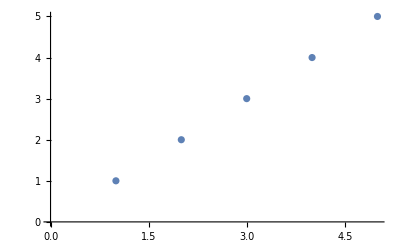

```mathematica
ListPlot[{1,2,3,4,5}]
```

Operadores sobre listas

Las listas son un símbolo más, de manera que todos los operadores que aplican sobre listas convierten la expresión a una función. El operador Part que nos permite acceder a elementos de listas es en realidad una función más.

```mathematica
FullForm[Hold[list[[i]]]]
```

Hold[Part[list,i]]

Los operadores que actúan sobre símbolos numéricos como enteros, reales, etc, (símbolos atómicos) también actúan sobre listas para realizar operaciones aritméticas. A menudo la regla general es que un operador que actúa sobre una lista y un símbolo atómico devuelve una lista donde se aplica el operador a cada uno de los elementos de la lista. Por ejemplo

```mathematica
??Plus
```

```mathematica
{1,2,3}+10
```

{11,12,13}

```mathematica
{1,2,3}*10
```

{10,20,30}

```mathematica
{1,2,3}^2
```

{1,4,9}

Mientras que un operador actuando sobre dos listas realiza la operación entre cada uno de los elementos de la lista.

```mathematica
{1,2,3}+{4,5,6}
```

{5,7,9}

```mathematica
{1,2,3}*{4,5,6}
```

{4,10,18}

```mathematica
{1,2,3}.{4,5,6}
```

32

#### Ejercicio 1:

Haga una gráfica con los números del 1 al 10 elevados al cuadrado.

#### Ejercicio 2:

Unas funciones especialmente para manipular listas son Take[], que permite seleccionar un número específico de elementos como por ejemplo

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Take[Alphabet[],6]
```

{a,b,c,d,e,f}

o Drop[] que permite descartar un número específico de elementos

```mathematica
Drop[Alphabet[],6]
```

{g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Drop[Alphabet[],-6]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t}

Apliquemos esto a finanzas. En esta área es común trabajar con los retornos de los precios, esto es, la diferencia diaria entre precios:

R_t = P_(t+1)- P_t

```mathematica
preciosGE = {50.,48.,47.918,48.552,50.438,50.417,50.5,50.667,51.25,50.333,49.333,49.573,48.646,48.042,46.042,46.167,47.146,47.25,44.667,44.667};
```

Haciendo uso de Drop[], obtener los retornos de los precios. Luego, volver a hacer lo mismo pero usando Take[]. El resultado esperado es:

{-2.,-0.0820007,0.633999,1.886,-0.0209999,0.0830002,0.167,0.583,-0.917,-1.,0.240002,-0.927002,-0.604,-2.,0.125,0.979,0.104,-2.583,0.}

Asignaciones

Existen dos tipos de operadores de asignación. El más común es el operador de asignación instantánea, lhs = rhs, que está representado por la función Set.

```mathematica
n = 5
```

5

```mathematica
n
```

5

```mathematica
FullForm[Hold[n=5]]
```

Hold[Set[n,5]]

Se caracteriza porque una vez asignado el valor del símbolo, este no cambiará de valor a no ser que se realice otra asignación. Esto es análogo a las asignaciones en otros lenguajes de programación.
El otro operador es el de asignación retardada, lhs := rhs, que se caracteriza por mantener rhs en forma no evaluada hasta que se requiera evaluar lhs. Para entender esto veamos el siguiente ejemplo.

Al ejecutar el siguiente código,

```mathematica
n = RandomReal[]
```

0.158515

n adquiere un valor que permanece fijo.

```mathematica
n
```

0.158515

Pero con una asignación retardada, n no adquiere ningún valor específico.

```mathematica
n := RandomInteger[10]
```

```mathematica
Range[n]
```

{1,2}

Entonces cada vez que queramos ver el valor de n, se llamará a la función RandomReal.

```mathematica
n
```

0.608173

```mathematica
n
```

0.0329449

La convención para nombrar símbolos es usar lowerCamelCase. La utilidad de asignaciones retardadas quedará más clara al ver el comportamiento de las funciones y reglas de sustitución.

Los operadores = y := son equivalentes a las funciones Set[] y SetDelayed[].

```mathematica
FullForm[Hold[a=b]]
```

Hold[Set[a,b]]

```mathematica
FullForm[Hold[a:=b]]
```

Hold[SetDelayed[a,b]]

#### Ejercicio:

Reemplazar x en

```mathematica
{x,x+1,x+2,x^2}
```

por un número entero aleatorio entre el 0 y 100 y que cada valor de x sea diferente

Iteradores y construcción de listas

El lenguaje Wolfram posee funciones para iterar sobre elementos o un rango numérico. La regla general es que si uno utiliza una estructura de control tipo For, While o Do, probablemente hay una ineficiencia en el diseño del código. El iterador más general es Table, que nos permite crear listas.

```mathematica
Table[i^2,{i,1,20}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

Nota

Esto contrasta con la forma de operar listas en otros lenguajes, que por lo general suele escribirse con la siguiente sintaxis (nótese la utilidad de la asignación retardada):

```mathematica
procedural :=Block[{i,outputList},
i= 1;
outputList = {};
While[i≤ 20,
AppendTo[outputList,i];
i++;
];
outputList
]

procedural
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Este tipo de programación, que se conoce como programación procedimental, no es adecuada para el lenguaje Wolfram. Esto queda más evidente cuando se mide el tiempo de ejecución:

```mathematica
tiempoProcedural = First[RepeatedTiming[procedural]]
```

0.000036

```mathematica
tiempoFuncional = First[RepeatedTiming[Table[i,{i,20}]]]
```

7.6×10^-6

```mathematica
100*N[tiempoProcedural/tiempoFuncional]
```

469.285

El aumento de velocidad es alrededor del 469 % !!!!!

Lo útil de las tablas es que dentro de ellas se pueden realizar operaciones arbitrarias

```mathematica
Table[i^2,{i,3,10}]
```

{9,16,25,36,49,64,81,100}

Table también nos permite iterar sobre listas

```mathematica
2*{1,3,4,2}
```

{2,6,8,4}

```mathematica
i = 6
```

6

```mathematica
Table[2*i^2+4,{i,{1,3,4,2}}]
```

{6,22,36,12}

Las tablas no están restringidas por número de iteradores, así que es completamente válido hacer

```mathematica
Table[10i+j,{i,1,5},{j,1,5}]
```

{{11,12,13,14,15},{21,22,23,24,25},{31,32,33,34,35},{41,42,43,44,45},{51,52,53,54,55}}

Nota

Uno de los usos comunes de Table es crear una lista con n elementos repetidos. Por ejemplo

```mathematica
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
ConstantArray[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
RandomColor[]
```

RGBColor[0.35964516145541636, 0.6771828717072874, 0.6181724861909921]

```mathematica
c := RandomColor[];
```

```mathematica
Table[c,10]
```

{RGBColor[0.37470956113251996, 0.33493908870158307, 0.4132030461494225],RGBColor[0.47120922204010407, 0.662760477342144, 0.30227740366659495],RGBColor[0.9640189461716484, 0.3406080873114177, 0.9488957715550916],RGBColor[0.17385145734638185, 0.38087086536416304, 0.7045107950994467],RGBColor[0.9702381791359938, 0.1614848167074916, 0.9777102719049926],RGBColor[0.6446696286965903, 0.11037041249105384, 0.8160157729628188],RGBColor[0.33624767580654136, 0.8887682470574236, 0.7535772762230055],RGBColor[0.11901643156958985, 0.9308941492425888, 0.5907495029305763],RGBColor[0.9177321637439588, 0.8124544955871895, 0.33812000181201807],RGBColor[0.1152283191797625, 0.9370637660047474, 0.7552613446218888]}

```mathematica
ConstantArray[c,10]
```

{RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928],RGBColor[0.7078036936736567, 0.8360026509526879, 0.9433189041834928]}

Evalúa 10 veces el número 1 lo que a efectos prácticos significa un array constante, ¡pero hay que tener cuidado! El argumento dentro de Table puede cambiar con cada evaluación de manera que podríamos obtener resultados erróneos. Si se evalúa una variable con una asignación retardada puede haber complicaciones.

```mathematica
c := RandomColor[];
```

```mathematica
Table[c,10]
```

{RGBColor[0.16978852873192074, 0.31843938210988876, 0.8336084603458491],RGBColor[0.8223790588815998, 0.7319023247476437, 0.8635252080105642],RGBColor[0.7197949115894258, 0.5686354886831095, 0.5111542518145891],RGBColor[0.13590796389940252, 0.2327206146187466, 0.7674260774506634],RGBColor[0.043429320371571434, 0.12770568740482546, 0.38888780466822825],RGBColor[0.7243019127243957, 0.8834897508241522, 0.2875346617541821],RGBColor[0.861976828618767, 0.4241354518715066, 0.5906095211970519],RGBColor[0.3569374015487208, 0.5684360355064291, 0.26524719573775135],RGBColor[0.6849398018376489, 0.8384334247152958, 0.34952067574291057],RGBColor[0.9062727380851534, 0.7346901715366165, 0.11169147574757665]}

En los casos que se desee especificar que la variable siempre debe tener el mismo valor es mejor usar ConstantArray[].

```mathematica
ConstantArray[c,10]
```

{RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935],RGBColor[0.9036810071327546, 0.43747545255559306, 0.3602728868628935]}

En una tabla el iterador puede ser cualquier variable, no hay limitación en el tipo de nombre siempre que tenga una sintaxis válida

```mathematica
Table[narvaez^2,{narvaez,0,3}]
```

{0,1,4,9}

#### Ejercicio 1:

A partir de la lista

```mathematica
l = {1,"hola",9/8,2.3}
```

{1,hola,9/8,2.3}

crear un snippet que obtenga el encabezado (Head) de cada elemento.

```mathematica
Table[Head[i],{i,l}]
```

{Integer,String,Rational,Real}

```mathematica
Table[Head[l[[i]]],{i,1,Length[l]}]
```

{Integer,String,Rational,Real}

#### Ejercicio 2:

```mathematica
Table[narvaez,{narvaez,-3,-10,-0.6}]
```

{-3.,-3.6,-4.2,-4.8,-5.4,-6.,-6.6,-7.2,-7.8,-8.4,-9.,-9.6}

Crear un snippet que genera la siguiente lista

```mathematica
{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}
```

#### Ejercicio 3:

Dadas dos listas

```mathematica
a={0,1,2,3,4};
b={5,6,7,8,9};
```

Escriba el código que devuelva

```mathematica
{{0,5},{1,6},{2,7},{3,8},{4,9}}
```

{{0,5},{1,6},{2,7},{3,8},{4,9}}

Nota: Hay dos formas eficientes de hacer esto. Puede ser útil buscar en la documentación, pero no es necesario.

Hint: Sólo es necesario usar un iterador

#### Ejercicio 4:

La función Column[] nos permite apilar elementos en una columna

```mathematica
Column[{3,5,7,1}]
```

3
5
7
1

Crear  una tabla que devuelva el siguiente resultado.

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8}

Ejercicios de repaso

### Ejercicio 1:

Crear tabla de multiplicación de los números del 1 al 5. Ordenarla visualmente utilizando Grid[].

### Ejercicio 2:

Visualizar la misma tabla de multiplicar usando ArrayPlot[].

### Ejercicio 3:

Circle[] es una primitiva gráfica que representa un círculo. Para poder visualizar las primitivas gráficas se utiliza Graphics[], como por ejemplo

```mathematica
Circle[]
```

Circle[{0,0}]

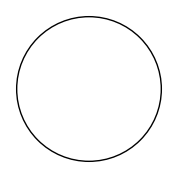

```mathematica
Graphics[Circle[]]
```

Las primitivas gráficas (como cualquier otro objeto simbólico) se pueden crear dentro de una tabla. Crear un array bidimensional de círculos de manera que quede

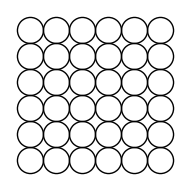

### Ejercicio 4:

Crear círculos concéntricos que se desplacen progresivamente hacia la izquierda.

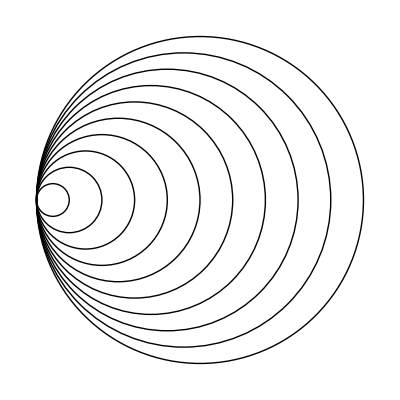

### Ejercicio 4.5:

Crear un patrón de interferencia de dos ondas

#### Solución:

```mathematica
a =Table[Circle[{i,0},i],{i,10}]
```

{Circle[{1,0},1],Circle[{2,0},2],Circle[{3,0},3],Circle[{4,0},4],Circle[{5,0},5],Circle[{6,0},6],Circle[{7,0},7],Circle[{8,0},8],Circle[{9,0},9],Circle[{10,0},10]}

```mathematica
b = Table[Circle[{i,10},i],{i,10}]
```

{Circle[{1,10},1],Circle[{2,10},2],Circle[{3,10},3],Circle[{4,10},4],Circle[{5,10},5],Circle[{6,10},6],Circle[{7,10},7],Circle[{8,10},8],Circle[{9,10},9],Circle[{10,10},10]}

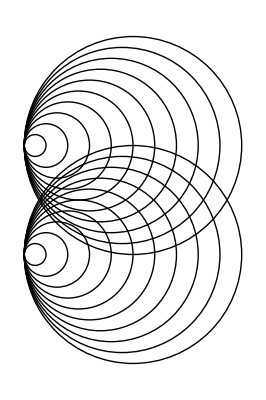

```mathematica
Graphics[Join[a,b]]
```

### Ejercicio 5:

Crear 100 círculos con posición y radio aleatorios en un intervalo de radio del 1 al 10 y de posición del 0 a 50.

Patrones y reglas de sustitución

Las reglas de sustitución son un aspecto central en el diseño del lenguaje Wolfram, de hecho, como se verá posteriormente, las funciones son un caso especial de una regla de sustitución con patrones. Este es uno de los puntos más fuertes del lenguaje debido a su gran flexibilidad y claridad. Esto contrasta mucho con la forma de manipular patrones de datos usando otros lenguajes.

Una técnica muy común en otros lenguajes de programación consiste en utilizar una sintaxis llamada expresiones regulares o regex, que no podría ser más endemoniadamente complicada. La siguiente expresión regular se usa para verificar si una cadena de texto corresponde a un correo electrónico válido.

/^([a-z0-9_\.-]+)@([\da-z\.-]+)\.([a-z\.]{2,6})$/

Mathematica puede trabajar con Regex, pero su uso es casi siempre innecesario.

```mathematica
StringCases["john@doe.com",RegularExpression["^([a-z0-9_\\.-]+)@([\\da-z\\.-]+)\\.([a-z\\.]{2,6})$"]]
```

{john@doe.com}

```mathematica
StringCases["john@doe.something",RegularExpression["^([a-z0-9_\\.-]+)@([\\da-z\\.-]+)\\.([a-z\\.]{2,6})$"]]
```

{}

La función más elemental para trabajar con patrones en forma nativa en el lenguaje Wolfram es MatchQ[], que se encarga de determinar si una expresión encaja con un patrón especificado. Por ejemplo

```mathematica
Clear[a,b]
```

```mathematica
MatchQ[{3,y,Circle[]},{_,x,_}]
```

False

Da un resultado afirmativo. En este ejemplo la función trata de emparejar la lista {a, x, b} con la lista {_, x, _}. El símbolo  _  representa un patrón vacío, es decir, un patrón donde cualquier expresión puede coincidir.

```mathematica
MatchQ[7,_]
```

True

Internamente al patrón _ se le conoce como patrón Blank[]

```mathematica
FullForm[_]
```

Blank[]

Los patrones son útiles para seleccionar elementos que cumplen cierto criterio, esto se hace con la función Cases[]

```mathematica
Cases[{{a,a},{b,b,a},{b,a},{a,b,b},{b,b},{c,b}},{b,_}]
```

{{b,a},{b,b}}

Pero la verdadera utilidad de los patrones es que con ellos podemos establecer reglas de sustitución, y esto es fundamental a la hora de hacer operaciones algebraicas o manipular grandes bases de datos. Para usar esta funcionalidad es necesario establecer una regla de sustitución que buscará un patrón. Un ejemplo de una regla de sustitución simple puede ser reemplazar todas las ocurrencias del número 1 por el número 2, donde el número 1 es el patrón a buscar que será reemplazado por el número 2.

```mathematica
FullForm[x->y]
```

Rule[x,y]

```mathematica
{1,2,3,4,1,9,8} /. 1->2
```

{2,2,3,4,2,9,8}

Aquí hay 2 de los 3 operadores básicos en patrones.    /. es el operador que representa a la función ReplaceAll, y -> Representa la función Rule.

```mathematica
FullForm[Hold[{1,2,3,4,1,9,8} /. 1->2]]
```

Hold[ReplaceAll[List[1,2,3,4,1,9,8],Rule[1,2]]]

El patrón underscore _ hace un match de cualquier tipo de expresión.

```mathematica
{1,2,3,4,1,9,8} /. _->3
```

3

```mathematica
x /. _->3
```

3

¿Para qué nos sirve este tipo de patrón? Resulta extremadamente útil cuando se requiere ignorar o reemplazar un elemento de una expresión. Por ejemplo

```mathematica
{{1,2},{3,7},{8,2},{5,0}} /. {_,2}->Nothing
```

{{3,7},{5,0}}

```mathematica
{{1,2},{3,7},{8,2},{5,0}} /. {_,2}->"reemplazado"
```

{reemplazado,{3,7},reemplazado,{5,0}}

El tercer operador básico es :> que representa a RuleDelayed. RuleDelayed es a Rule lo que SetDelayed (:=) es a Set (=). Es útil cuando se desea aplicar transformaciones dentro de un patrón. Pongamos un ejemplo.

El patrón x_ es similar a _ con la diferencia de que guarda temporalmente el símbolo correspondiente en x. Al reemplazar con símbolos es más recomendable usar RuleDelayed. Por ejemplo

```mathematica
FullForm[x:> y]
```

RuleDelayed[x,y]

```mathematica
{{2,2},{3,7},{8,2},{5,0}} /. {x_,2}:>{x^2,2}
```

{{4,2},{3,7},{64,2},{5,0}}

Los patrones sirven como una alternativa a regex para hacer búsquedas dentro de listas.

```mathematica
Cases[{f[2],g[2],f[5],g[3]},f[_]]
```

{f[2],f[5]}

Otra forma de hacer esto es usando el patrón _h, donde h es el encabezado de una función.

```mathematica
Cases[{f[1],g[2],f[5],g[3]},_f]
```

{f[1],f[5]}

#### Ejercicio 1:

Para buscar patrones a través del encabezado se puede usar el patrón _h, que por ejemplo, encuentra todas las expresiones con encabezado h. Escriba un código que a partir de la lista

```mathematica
{1, 1, f[a], 2, 3, y, f[8], 9, f[10]}
```

devuelva

```mathematica
{f[a], f[8], f[10]}
```

usando patrones.

#### Ejercicio 2:

Escriba un código que a partir de la misma lista

```mathematica
{1, 1, f[a], 2, 3, y, f[8], 9, f[10]}
```

extraiga los argumentos de la función f.

```mathematica
Cases[{1, 1, f[a], 2, 3, y, f[8], 9, f[10]},f[i_]:>i]
```

{a,8,10}

#### Proyecto: Visualización de dígitos de π

En este mini-proyecto se hará una visualización simple de los dígitos de π a través de reglas de sustitución que cambien cada dígito a un color. El proyecto se dividirá en pequeños problemas.

1. Dentro del lenguaje Wolfram existen colores predefinidos que se pueden usar directamente en el código. Por ejemplo

```mathematica
Black
```

GrayLevel[0]

También existen funciones que representan gradientes de colores, como

```mathematica
ColorData["Rainbow"][0.3]
```

RGBColor[0.2979596, 0.5657928, 0.7522386000000001]

```mathematica
ColorData["Rainbow"][0.7]
```

RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976]

Estas funciones se pueden encontrar dentro del menú Paletas->Esquemas de color.
Construye una lista de 10 colores diferentes utilizando un gradiente. El resultado esperado es algo similar al siguiente:

```mathematica
colores = Table[ColorData["Rainbow"][i],{i,0.1,1,0.1}]
```

{RGBColor[0.2748608, 0.18226360000000003, 0.7272788],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.29795960000000005, 0.5657928, 0.7522386],RGBColor[0.38822480000000004, 0.674195, 0.6035436],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660832, 0.7430418, 0.32293540000000004],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2748608, 0.18226360000000003, 0.7272788],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.29795960000000005, 0.5657928, 0.7522386],RGBColor[0.38822480000000004, 0.674195, 0.6035436],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.6660832000000002, 0.7430418, 0.32293539999999993],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.8929546, 0.38966159999999994, 0.1794008]}
```

2. Ahora se desea crear una regla de sustitución que asigne cada color a un dígito. Es posible realizarlo a mano, pero al programar siempre se debe evitar algo así. Una función que nos puede servir es Thread, que se encarga de aplicar una función a cada uno de sus argumentos iterando sobre elementos del mismo índice.

```mathematica
Thread[f[{a,b,c},{x,y,z}]]
```

{f[a,x],f[b,y],f[c,z]}

Conociendo que una regla tiene el equivalente en función Rule[], obtenga la siguiente lista de forma programática (sin hacerlo a mano).

```mathematica
{0->RGBColor[0.471412, 0.108766, 0.527016],1->RGBColor[0.2748608, 0.18226360000000003, 0.7272788],2->RGBColor[0.2484884, 0.3863264, 0.813373],3->RGBColor[0.29795960000000005, 0.5657928, 0.7522386],4->RGBColor[0.38822480000000004, 0.674195, 0.6035436],5->RGBColor[0.513417, 0.72992, 0.440682],6->RGBColor[0.6660832000000002, 0.7430418, 0.32293539999999993],7->RGBColor[0.8083416, 0.7110806, 0.255976],8->RGBColor[0.8935136, 0.6004149999999999, 0.2205464],9->RGBColor[0.8929546, 0.38966159999999994, 0.1794008]}
```

```mathematica
FullForm[Hold[Range[0,9]->colores]]
```

Hold[Rule[Range[0,9],colores]]

```mathematica
regla = Thread[Range[0,9]->colores]
```

{0→RGBColor[0.2748608, 0.18226360000000003, 0.7272788],1→RGBColor[0.2484884, 0.3863264, 0.813373],2→RGBColor[0.29795960000000005, 0.5657928, 0.7522386],3→RGBColor[0.38822480000000004, 0.674195, 0.6035436],4→RGBColor[0.513417, 0.72992, 0.440682],5→RGBColor[0.6660832, 0.7430418, 0.32293540000000004],6→RGBColor[0.8083416, 0.7110806, 0.255976],7→RGBColor[0.8935136, 0.6004149999999999, 0.2205464],8→RGBColor[0.8929546, 0.38966159999999994, 0.1794008],9→RGBColor[0.857359, 0.131106, 0.132128]}

3. Los dígitos de π los podemos obtener con la función RealDigits[]

```mathematica
piDigits = First[RealDigits[π,10,10000]];
```

```mathematica
piColoreado = piDigits/.regla;
```

```mathematica
Take[piColoreado,10]
```

{RGBColor[0.38822480000000004, 0.674195, 0.6035436],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.6660832, 0.7430418, 0.32293540000000004],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.29795960000000005, 0.5657928, 0.7522386],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.6660832, 0.7430418, 0.32293540000000004],RGBColor[0.38822480000000004, 0.674195, 0.6035436]}

Donde el primer argumento son los dígitos y el último el exponente del número. Reemplace una lista de 10000 dígitos de π con la regla de sustitución de colores calculada anteriormente. Nota: Visualizar colores es una operación tardada, ya que son elementos gráficos. Puede ser útil cortar el resultado usando la función Take.

4. Ahora queremos mostrar los dígitos coloreados en una gráfica. Para esto podemos utilizar ArrayPlot[]

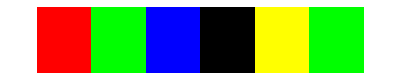

```mathematica
ArrayPlot[{{Red,Green,Blue,Black,Yellow,Green}}]
```

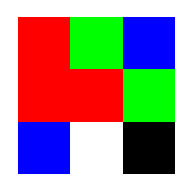

```mathematica
ArrayPlot[{{Red,Green,Blue},{Red,Red,Green},{Blue,White,Black}}]
```

El problema es que para que la gráfica no se vea como una lista interminable de colores debemos formatear la lista de dígitos coloreados para que adquiera forma de matriz, que son listas anidadas.

```mathematica
{{Red,Green,Blue},{Red,Red,Green},{Blue,White,Black}}
```

{{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[0]}}

Una forma eficiente de hacer esto es utilizando la función Partition[], que como su nombre lo dice, se encarga de hacer particiones de los elementos de una lista.

```mathematica
Partition[Alphabet[],5]
```

{{a,b,c,d,e},{f,g,h,i,j},{k,l,m,n,o},{p,q,r,s,t},{u,v,w,x,y}}

Cree particiones de 100 en 100 de la lista de dígitos coloreados y grafíquelos con ArrayPlot.

Funciones

Imaginemos ahora que queremos crear una regla de sustitución que al detectar f[x] toma el argumento de f y lo sustituye por x^2. Esto en esencia es la definición de una función.

```mathematica
f[5]/.f[x_]:>x^2
```

25

Se intuye entonces que una función puede ser descrita como una regla de sustitución, y es de hecho así como operan las funciones en el lenguaje Wolfram. La sintaxis de una función consiste en realizar una sustitución a partir de una asignación retardada.

Por ejemplo, vamos a definir una función f que acepte un argumento x y devuelva x^2. Se define la función,

```mathematica
f[x_]:=x^2;
```

y se puede evaluar con la notación []  ,

```mathematica
f[7]
```

49

utilizando el operador prefix,

```mathematica
f@4
```

16

o utilizando el operador postfix.

```mathematica
4 // f
```

16

Por legibilidad es preferible utilizar la notación [].

```mathematica
f[9]
```

81

Es posible definir una función que opere sólo sobre un tipo específico de argumento. Para ello utilizamos el patrón _h que se encarga de verificar si el encabezado del argumento coincide con el patrón especificado en la función.

```mathematica
Clear[f]
```

```mathematica
f[x_Integer]:=x^2;
f[5]
f[1.5]
```

25

f[1.5]

Al definir esta función lo que se está haciendo en realidad es crear una regla que especifica que cada vez que se encuentre la expresión f[ ] se extraerá el símbolo x y se sustituirá por x^2, y por último se procede a evaluar el resultado. De esta forma la definición de una función es tan flexible como los patrones. Esta es una de las características más poderosas del lenguaje.
Se puede definir una función con un número finito de argumentos,

```mathematica
f[x_,y_,z_]:=x+y+z;
f[3,4,1]
```

8

una función con un número arbitrario de argumentos,

```mathematica
f[n__]:=Total[List[n]];
f[1,2,3,4,5]
f[1,2,3,4,5,6,7]
```

15

28

e incluso se pueden definir las funciones de forma ascendente (la notación para esto es ^:= ).

```mathematica
Exp[g[x_]]^:=StringJoin["El símbolo x vale: ",ToString[x]];
```

```mathematica
Exp[g[9]]
```

El símbolo x vale: 9

Dado que las funciones se comportan como patrones, es posible asignar resultados a valores específicos de una función. Por ejemplo, al evaluar la siguiente función, dado que f no está definida, el kernel devuelve la forma simbólica de la función.

```mathematica
Clear[f]
```

```mathematica
{f[Blue],f[Green],f[Black],f[Red],f[Yellow],f[Orange]}
```

{f[RGBColor[0, 0, 1]],f[RGBColor[0, 1, 0]],f[GrayLevel[0]],f[RGBColor[1, 0, 0]],f[RGBColor[1, 1, 0]],f[RGBColor[1, 0.5, 0]]}

Pero si asignamos algunos valores de f y reevaluamos se obtiene una lista con los valores definidos ya evaluados

```mathematica
f[Blue]= "Color azul";
f[Red]= "Color rojo";
{f[Blue],f[Green],f[Black],f[Red],f[Yellow],f[Orange]}
```

{Color azul,f[RGBColor[0, 1, 0]],f[GrayLevel[0]],Color rojo,f[RGBColor[1, 1, 0]],f[RGBColor[1, 0.5, 0]]}

Nótese que aquí se utilizó la asignación instantánea.
El poder definir una función de diferentes formas nos permite hacer lo que en otros lenguajes se conoce como sobrecarga de funciones, que es asociar una función con implementaciones múltiples que operan sobre diferentes tipos de datos. Un ejemplo es la definición de la función factorial que se puede definir de forma recursiva hasta llegar al último número donde aplica una definición especial.

```mathematica
factorial[n_Integer]:=n * factorial[n-1];
factorial[1] = 1;
```

```mathematica
factorial[20]
```

2432902008176640000

```mathematica
First[RepeatedTiming[factorial[50]]]
```

0.000066

En otros lenguajes la forma equivalente es:

```mathematica
Clear[factorial]
```

```mathematica
factorial[n_Integer]:=If[n ≠ 1,n * factorial[n-1],1];
```

```mathematica
factorial[20]
```

2432902008176640000

```mathematica
First[RepeatedTiming[factorial[50]]]
```

0.000099

Esta forma es ligeramente más lenta debido a la presencia del If en cada iteración.

Nota

La forma en la que el lenguaje Wolfram trata a las funciones es fundamentalmente diferente a otros lenguajes. En otros lenguajes una función representa un salto en la ejecución de un programa, donde al llamar la función primero se copian los argumentos al stack (memoria), luego ocurre un salto en la posición de la ejecución del programa, y al terminar la ejecución de la función vuelve a haber otro salto hacia la posición de ejecución anterior.

En el lenguaje Wolfram el enfoque consiste en que las funciones son reglas de sustitución y al evaluar una sección de código se aplican todas las reglas de sustitución necesarias hasta llegar a las funciones internas definidas en el kernel. Entonces el kernel evalúa las funciones desde la función más profunda hasta la más externa.

Por ejemplo:

```mathematica
A[x_]:= Hold[g[x]];
NestedFunc[num_]:= NestList[A[#]&,4,num];
```

```mathematica
FullForm[NestedFunc[4]]
```

List[4,Hold[g[4]],Hold[g[Hold[g[4]]]],Hold[g[Hold[g[Hold[g[4]]]]]],Hold[g[Hold[g[Hold[g[Hold[g[4]]]]]]]]]

#### Ejercicio 1:

El código

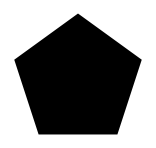

```mathematica
Graphics[Polygon[CirclePoints[5]]]
```

nos devuelve un polígono regular de 5 lados. Crear una función llamada Poly que devuelva un polígono regular de n lados, y luego evaluar esta función en una tabla con n que va desde 3 hasta 10.

#### Ejercicio 2:

Defina una función fibonacci[n_Integer] usando sobrecarga de funciones. Tip: fibonacci[n_Integer] es la suma de dos evaluaciones de fibonacci[] con diferentes argumentos. Nota: Debe definirse en minúsculas ya que Mathematica ya trae implementada una función Fibonacci[n] que hace exactamente lo mismo.

Técnicas para el uso de funciones

En algunos casos es necesario aplicar cada elemento de una lista como argumento de una función.  Regresemos al ejemplo donde

```mathematica
f[x_,y_,z_]:=x+y+z;
```

Si se desea que el argumento sea cada elemento de la lista

```mathematica
l = {3,2,9}
```

{3,2,9}

una manera poco elegante de hacer esto es pasando manualmente cada argumento.

```mathematica
f[l[[1]],l[[2]],l[[3]]]
```

14

pero existe una manera más eficiente utilizando la función Apply,

```mathematica
Apply[f,l]
```

14

que además cuenta con una notación de operador prefix

```mathematica
f @@ l
```

14

Apply funciona cambiando el encabezado en la expresión por el especificado.

```mathematica
FullForm[l]
```

List[3,2,9]

```mathematica
Clear[f]
```

```mathematica
FullForm[Apply[f,l]]
```

f[3,2,9]

Por defecto, en el lenguaje Wolfram todo pertenece al espacio global, esto significa que es posible declarar funciones impuras, esto es, funciones que causan efectos secundarios como por ejemplo

```mathematica
a = 1;
```

```mathematica
a
```

1

```mathematica
f[x_]:= a = x;
```

```mathematica
f[3]
```

3

```mathematica
a
```

3

En este lenguaje esto es considerado una mala práctica y por lo general debe ser evitado. Una manera de localizar los símbolos es utilizar la función Module.

```mathematica
a
```

3

```mathematica
f[x_]:= Module[{a},
a = x;
a += 1;
Return[a];
];
```

```mathematica
f[7]
```

8

```mathematica
a
```

3

#### Ejercicio 1:

Definamos la función factorial de forma diferente. Otro enfoque consiste en crear una lista de tamaño n con números sucesivos, por ejemplo

```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

Y multiplicarlos todos. Para hacer esto es necesario aplicar una función que se encargue de multiplicar sus argumentos. Tip: Puede ser útil investigar que función multiplica usando FullForm.

#### Ejercicio 2:

Lo malo de hacer sobrecarga de funciones es que todas las múltiples definiciones se quedan en el espacio global. En el ejercicio de Fibonacci que se resolvió en la sección anterior tenemos que una solución es:

```mathematica
fibonacci[n_]:=fibonacci[n-1] + fibonacci[n-2];
fibonacci[1] = 1;
fibonacci[0] = 1;
```

Todas estas definiciones quedan en el espacio global. Esto lo podemos verificar utilizando el operador ? (¡cuidado!, no confundir con _?) que representa la función Definition[] que se encarga de devolver información sobre las definiciones de funciones.

```mathematica
?fibonacci
```

Global`fibonacci

fibonacci[0]=1
 
fibonacci[1]=1
 
fibonacci[n_]:=fibonacci[n-1]+fibonacci[n-2]

Hagamos borrón y cuenta nueva

```mathematica
Clear[fibonacci]
```

y tratemos de definir una función única que se encargue de calcular el número n-avo de fibonacci utilizando Module[].

#### Solución:

```mathematica
FibbModule[n_]:= Module[{fibonacci},
fibonacci[i_]:=fibonacci[i-1] + fibonacci[i-2];
fibonacci[1] = 1;
fibonacci[0] = 1;
fibonacci[n]
];
```

Mapeos

Una de las filosofías del lenguaje Wolfram es que es un lenguaje funcional. Esto significa que está diseñado para que se programe usando funciones generales que se aplican sobre listas, matrices, tensores, etc. La función más elemental de este tipo de lenguajes es el mapeo, que aquí está representado por la función Map.

```mathematica
Clear[a,f]
```

```mathematica
Map[f,{a,b,c,d,e}]
```

{f[a],f[{5,6,7,8,9}],f[c],f[d],f[e]}

El mapeo también se puede representar con la notación de operador infix,

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[{5,6,7,8,9}],f[c],f[d],f[e]}

aunque no es recomendable para código de producción, pero sí es útil para prototipos. La ventaja de Map es que se puede aplicar a un nivel arbitrario. Por ejemplo, en la lista {{a,b},{c,d,e}} podemos aplicar Map en el nivel superior

```mathematica
Map[f,{{a,b},{c,d,e}}]
```

{f[{a,{5,6,7,8,9}}],f[{c,d,e}]}

Al nivel 2

```mathematica
Map[f,{{a,b},{c,d,e}},{2}]
```

{{f[a],f[{5,6,7,8,9}]},{f[c],f[d],f[e]}}

e incluso en los niveles 1 y 2 simultáneamente.

```mathematica
Map[f,{{a,b},{c,d,e}},2]
```

{f[{f[a],f[{5,6,7,8,9}]}],f[{f[c],f[d],f[e]}]}

La verdadera ventaja de los mapeos es la capacidad del lenguaje de definir funciones anónimas y poder aplicarlas a una lista. Las funciones puras se definen a través del operador postfix Function (  &  ) y el operador Slot (  #  ).

```mathematica
FullForm[#^2 &]
```

Function[Power[Slot[1],2]]

Por ejemplo, una función pura que eleva el argumento al cuadrado puede ser

```mathematica
(#^2)&[5]
```

25

El slot actúa como el lugar donde se sustituirá el argumento, y el operador Function actúa convirtiendo todo lo que le precede en una función. Es posible también utilizar varios argumentos numerando los slots.

```mathematica
(#1^2 + #2^3)&[5,9]
```

754

La utilidad principal de las funciones anónimas es que nos proveen de una manera rápida de aplicar transformaciones sobre listas de una forma más flexible que Table.

```mathematica
Map[#^2&,Range[10]]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
l = Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
MapAt[#^2&,l,{All,2}]
```

{{1,4},{3,16},{5,36},{7,64},{9,100}}

Una de las aplicaciones prácticas más comunes de los mapeos es evaluar una función con un argumento constante

```mathematica
Map[f[#,3]&,{a,b,c}]
```

{f[a,3],f[{5,6,7,8,9},3],f[c,3]}

#### Ejercicio 1:

A partir de la lista

```mathematica
Partition[Alphabet[],2]
```

{{a,b},{c,d},{e,f},{g,h},{i,j},{k,l},{m,n},{o,p},{q,r},{s,t},{u,v},{w,x},{y,z}}

Obtener

{{b,a},{d,c},{f,e},{h,g},{j,i},{l,k},{n,m},{p,o},{r,q},{t,s},{v,u},{x,w},{z,y}}

Y luego obtener

{{z,y},{x,w},{v,u},{t,s},{r,q},{p,o},{n,m},{l,k},{j,i},{h,g},{f,e},{d,c},{b,a}}

#### Ejercicio 2:

Utilizando funciones puras y la función Select encuentre los elementos de la lista del tipo f[_] para la lista

```mathematica
{1, 1, f[a], 2, 3, y, f[8], 9, f[10]}
```

{1,1,f[a],2,3,y,f[8],9,f[10]}

#### Ejercicio 3:

Framed es una función que devuelve su argumento enmarcado. Por ejemplo:

```mathematica
Framed[3]
```

3

Utilizando las funciones If, PrimeQ, Framed, Range y Map cree una lista que enmarque a todos los número primos entre el 1 y 30.

Funciones anidadas

Hay ocasiones en las que uno desea aplicar sucesivamente una función  sobre si misma n veces. En matemáticas a esto se le conoce como composición de funciones.

```mathematica
Composition[f,g,h][x,y]
```

f[g[h[x,y]]]

Si queremos aplicar 3 veces una función f haríamos

```mathematica
Composition[f,f,f][x]
```

f[f[f[x]]]

Lo cual se puede generalizar a una aplicación sucesiva durante n veces

```mathematica
FuncionAnidada[f_,arg_,n_]:=Apply[Composition,Table[f,n]][arg]
```

```mathematica
FuncionAnidada[f,x,10]
```

f[f[f[f[f[f[f[f[f[f[x]]]]]]]]]]

El lenguaje Wolfram nos ofrece una forma nativa de realizar este tipo de operaciones con la función Nest, que es equivalente a la que acabamos de crear, pero mucho más rápida.

```mathematica
Nest[f,x,10]
```

f[f[f[f[f[f[f[f[f[f[x]]]]]]]]]]

```mathematica
100*N[First[RepeatedTiming[FuncionAnidada[f,x,10]]]/First[RepeatedTiming[Nest[f,x,10]]]]
```

303.716

A veces es útil anidar funciones mientras se anota el resultado de las evaluaciones en cada anidación. Para esto tenemos las función NestList[]

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

Las funciones anidadas pueden operar sobre cualquier tipo de datos:

```mathematica
NestList[Labeled[Framed[#],"Imagen recursiva",Top]&,"Comenzamos",10]
```

{Comenzamos,ComenzamosImagen recursiva,ComenzamosImagen recursivaImagen recursiva,ComenzamosImagen recursivaImagen recursivaImagen recursiva,ComenzamosImagen recursivaImagen recursivaImagen recursivaImagen recursiva,ComenzamosImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursiva,ComenzamosImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursiva,ComenzamosImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursiva,ComenzamosImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursiva,ComenzamosImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursiva,ComenzamosImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursivaImagen recursiva}

#### Ejercicio 1:

El mapeo logístico es un mapeo discreto que es notable por su aparente simplicidad y complejidad de la dinámica. Está definido como un mapeo recurrente dado por

x_(n+1) = r x_n(1-x_n)

Esta ecuación implica que podemos definir el mapeo como una sucesión de aplicaciones de una función f(x_n) dada por

f(x_n) = r x_n(1-x_n)

donde la n-ésima iteración estará dada por una composición de n aplicaciones de la función f. Haciendo que r=4, calcule y grafique la dinámica del mapeo logístico para un valor inicial x_0 = 0.25 durante  50 iteraciones.

#### Ejercicio 2:

Cree una función Logistic[r_, iter_] que calcule la dinámica descrita en el ejercicio 1 pero con un valor de r arbitrario y un número iter de iteraciones. Luego haga una tabla con los resultados de Logistic usando 500 iteraciones y su respectivo valor de r y grafique con ListPlot[].

Será necesario organizar los elementos de la tabla tal que en vez de que se obtenga algo como {r, x_1, x_2, ... , x_n} se obtenga {{r,x_1}, {r,x_2}, ... {r, x_n}}. Para esto es útil la función Thread[]. Quizás obtenga mejores resultados si desecha las 20 primeras iteraciones usando Drop[].

```mathematica
Thread[{1,Range[10]}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10}}

#### Proyecto:

Ningún algoritmo puede generar números realmente aleatorios, sin embargo en todos los lenguajes de programación existen funciones como

```mathematica
RandomReal[]
```

0.648509

que aparentemente son capaces de generar dichos números. En realidad, lo que generan estas funciones son números pseudoaleatorios, creados por un algoritmo tan caótico que a efectos prácticos parece aleatorio. Uno de los algoritmos más comúnmente utilizados es el Lineal Congruential Generator (LCG), que es extremadamente simple y al mismo tiempo genera números aleatorios de buena calidad.
En el LCG, dada una semilla x_0, el siguiente valor de x está dado por

x_(n+1)= (a x_n + c) % m

donde % es la operación módulo y a, c y m son números enteros. En la función rand() definida en el compilador GCC del proyecto GNU los parámetros que utiliza son a = 1103515245, c = 0, m = 2^31. La selección de estos parámetros no es trivial, de hecho una mala selección puede tener consecuencias catastróficas. En los años 60, IBM diseñó una computadora llamada IBM System/360, y como toda computadora útil tenía que ofrecer funciones para generar números aleatorios. Los ingenieros decidieron utilizar unos cuantos hacks para acelerar la ejecución del código. Escogieron los siguientes parámetros:

- M = 2^31 para evitar calcular el resto: dividir por potencias de dos en computación es equivalente a encender o apagar determinados bits.

- A = 0 para ahorrar una suma.

- B = 65539 porque 65539 = 2^16 + 3, de nuevo simplifica las operaciones en binario.

A este algoritmo se le llamó RANDU y ha pasado a la historia por ser tan infame que la mitad de los papers que fueron desarrollados con simulaciones en esta computadora reportaron resultados falsos por culpa del algoritmo. ¿Pero qué tiene RANDU de especial?

El proyecto consiste en implementar el algoritmo LCG y comparar los resultados generados utilizando los parámetros que utiliza GCC y los parámetros de RANDU. Una técnica común para analizar la calidad de números aleatorios es una prueba espectral, que consiste en agrupar los números aleatorios (por ejemplo agruparlos de 2 en 2 o de 3 en 3) y graficarlos.

Para hacer este proyecto es posible que sea necesario usar las funciones: Mod, NestList, ListPointPlot3D y Partition.

Comentarios finales

La sintaxis del lenguaje Wolfram es compleja, y las reglas que utiliza no son triviales. Como sugerencia se recomienda no abusar de los operadores, suele ser mucho más fácil de leer

```mathematica
Apply[g,Map[f,Range[10]]]
```

g[f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]]

que

```mathematica
g @@ (f[#]&)/@ Range[10]
```

g[f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]]

a pesar de que ambos dan el mismo resultado. Además el segundo tipo de sintaxis es más vulnerable a errores. El siguiente código es similar pero devuelve un resultado muy diferente:

```mathematica
g @@ f[#]&/@ Range[10]
```

{g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10]}

También es recomendable utilizar lo más que se pueda las estructuras iterativas como Table y Map en vez de iteradores tradicionales como For, While y Do, y por último recordar que muchos de los algoritmos comúnmente usados ya han sido implementados, y nunca está de más buscar y rebuscar entre la documentación.

En caso de duda acerca del funcionamiento interno del lenguaje se puede consultar el enlace

http://reference.wolfram.com/language/tutorial/SomeNotesOnInternalImplementation.html

donde se discute más a fondo algunos detalles de la implementación. En caso de que esto no sea suficiente también se puede consultar la documentación y el código de Mathics, que es una implementación de código abierto del lenguaje Wolfram. 

https://mathics.github.io/

Si bien por ahora carece de muchas funciones es extremadamente útil para investigar funcionamientos no documentados.
El diagrama de clases de Mathics es especialmente útil para entender la jerarquía interna del programa.

-Graphics-